# Miller geometries

## Setting up the relevant equations

First let us note down the parameterization of the flux surface, and we will calculate the Jacobian. These will be used in the rest of the analysis. All the various replacements here are made to highlight that δ, sδ, etc... are all independent variables after our expansion.

```mathematica
Clear["Global`*"]
$Assumptions:={r>0,κ>0,ϵ>0,R0>0,Element[θ,Reals]}
ReplaceMiller={δ'[r]->sδ*(√(1-δ^2))/r,κ'[r]->sκ*κ/r,R0'[r]->dR0dr,δ[r]->δ,κ[r]->κ,R0[r]->R0}
FortranList={θ->theta,κ->kappa,sκ->skappa,sδ->sdelta,α->alpha,ϵ-> epsilon,q0->q,γ->gamma};
MillerPaper={κ->1.66,ϵ->1/3.17,δ->0.416,sκ->0.70,sδ->1.37,dR0dr->-0.354}
```

{δ'[r]→(sδ √(1-δ^2))/r,κ'[r]→(sκ κ)/r,R0'[r]→dR0dr,δ[r]→δ,κ[r]→κ,R0[r]→R0}

{κ→1.66,ϵ→0.315457,δ→0.416,sκ→0.7,sδ→1.37,dR0dr→-0.354}

## Geometry components

```mathematica
Rs=R0[r]+r*Cos[θ+(ArcSin[δ[r]]*Sin[θ])];
Zs=κ[r]*r*Sin[θ];
Jac=FullSimplify[Rs*(D[Rs,r]*D[Zs,θ]-D[Rs,θ]*D[Zs,r])/.ReplaceMiller]/.{r->ϵ*R0}
Clear[Rs,Zs]
Rs=R0+R0*ϵ*Cos[θ+(ArcSin[δ]*Sin[θ])]
Zs=R0*κ*ϵ*Sin[θ]
```

R0 ϵ κ (R0+R0 ϵ Cos[θ+ArcSin[δ] Sin[θ]]) (Cos[θ] (dR0dr+Cos[θ+ArcSin[δ] Sin[θ]])+(1+sκ-sδ Cos[θ]+(1+sκ) ArcSin[δ] Cos[θ]) Sin[θ] Sin[θ+ArcSin[δ] Sin[θ]])

R0+R0 ϵ Cos[θ+ArcSin[δ] Sin[θ]]

R0 ϵ κ Sin[θ]

```mathematica
Rc=FullSimplify[((D[Rs,θ]^2+D[Zs,θ]^2)^(3/2))/(D[Rs,{θ,1}]*D[Zs,{θ,2}]-D[Rs,{θ,2}]*D[Zs,{θ,1}])]
```

(R0 ϵ (κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2)^(3/2))/(κ (Cos[ArcSin[δ] Sin[θ]]+ArcSin[δ] Cos[θ]^2 (2+ArcSin[δ] Cos[θ]) Cos[θ+ArcSin[δ] Sin[θ]]))

```mathematica
sinu=FullSimplify[D[Zs,θ]*1/(√(D[Zs,θ]^2+D[Rs,θ]^2))]
```

(κ Cos[θ])/(√(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2))

```mathematica
cosu=FullSimplify[-D[Rs,θ]*1/(√(D[Zs,θ]^2+D[Rs,θ]^2))]
```

((1+ArcSin[δ] Cos[θ]) Sin[θ+ArcSin[δ] Sin[θ]])/(√(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2))

```mathematica
lθ=FullSimplify[√(D[Zs,θ]^2+D[Rs,θ]^2)]
```

R0 ϵ √(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2)

## The magnetic field

```mathematica
bp=FullSimplify[R0*(√(D[Rs,θ]^2+D[Zs,θ]^2))/Jac]
```

(√(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2))/(κ (1+ϵ Cos[θ+ArcSin[δ] Sin[θ]]) (Cos[θ] (dR0dr+Cos[θ+ArcSin[δ] Sin[θ]])+(1+sκ-sδ Cos[θ]+(1+sκ) ArcSin[δ] Cos[θ]) Sin[θ] Sin[θ+ArcSin[δ] Sin[θ]]))

We visually verify if this expression for the poloidal field is the same as in Miller (1998);

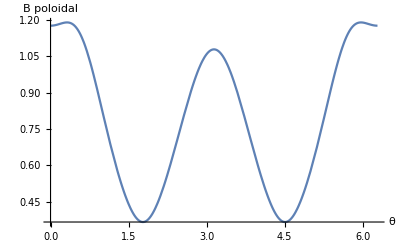

```mathematica
Plot[bp/.MillerPaper,{θ,0,2π},AxesLabel->{"θ","B poloidal"}]
```

```mathematica
bt=FullSimplify[R0/Rs]
```

1/(1+ϵ Cos[θ+ArcSin[δ] Sin[θ]])

## Normalize the quantities

```mathematica
Rshat=FullSimplify[Rs/R0]
Zshat=FullSimplify[Zs/R0]
Rchat=FullSimplify[Rc/(R0*ϵ)]
lθhat=FullSimplify[lθ/(R0*ϵ)]
```

1+ϵ Cos[θ+ArcSin[δ] Sin[θ]]

ϵ κ Sin[θ]

((κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2)^(3/2))/(κ (Cos[ArcSin[δ] Sin[θ]]+ArcSin[δ] Cos[θ]^2 (2+ArcSin[δ] Cos[θ]) Cos[θ+ArcSin[δ] Sin[θ]]))

√(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2)

## Some quick plots for verification

Let us plot the inverse radius of curvature to check the sign convention, and see if it makes sense

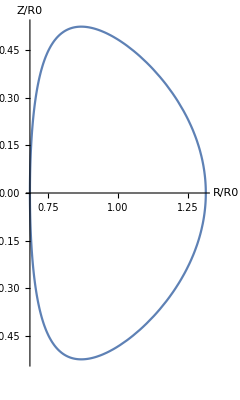

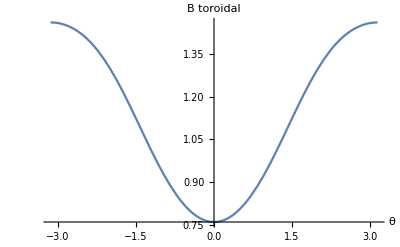

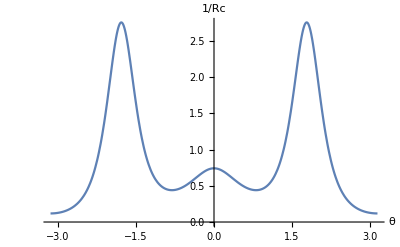

```mathematica
ParametricPlot[{Rshat,Zshat}/.MillerPaper,{θ,-π,π},AxesLabel->{"R/R0","Z/R0"}]
Plot[bt/.MillerPaper,{θ,-π,π},AxesLabel->{"θ","B toroidal"}]
Plot[1/Rchat/.MillerPaper,{θ,-π,π},AxesLabel->{"θ","1/Rc"}]
```

## Set up equation for the shear

```mathematica
fpR0eq=fpR0/.Solve[s==(γ*ϵ^2)/q*fpR0-2/γ*C1-(2*ϵ)/γ*C2-α/(2*γ*ϵ)*C3+q/γ^2*C4*fpR0,fpR0][[1]]
```

(-C3 q α γ-4 C1 q γ ϵ-2 q s γ^2 ϵ-4 C2 q γ ϵ^2)/(-2 C4 q^2 ϵ-2 γ^3 ϵ^3)

## Export to Fortran

```mathematica
FortranForm[FullSimplify[lθhat/.{ArcSin[δ]->x}]/.FortranList]
```

Sqrt(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)

```mathematica
FortranForm[FullSimplify[Rchat/.{ArcSin[δ]->x}]/.FortranList]
```

(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)**1.5/
     -  (kappa*(Cos(x*Sin(theta)) + x*Cos(theta)**2*(2 + x*Cos(theta))*Cos(theta + x*Sin(theta))))

```mathematica
FortranForm[FullSimplify[Rshat/.{ArcSin[δ]->x}]/.FortranList]
```

1 + epsilon*Cos(theta + x*Sin(theta))

```mathematica
FortranForm[FullSimplify[bp/.{ArcSin[δ]->x}]/.FortranList]
```

Sqrt(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)/
     -  (kappa*(1 + epsilon*Cos(theta + x*Sin(theta)))*(Cos(theta)*(dR0dr + Cos(theta + x*Sin(theta))) + 
     -      (1 + skappa + (-sdelta + x + skappa*x)*Cos(theta))*Sin(theta)*Sin(theta + x*Sin(theta))))

```mathematica
FortranForm[FullSimplify[sinu/.{ArcSin[δ]->x}]/.FortranList]
```

(kappa*Cos(theta))/Sqrt(kappa**2*Cos(theta)**2 + (1 + x*Cos(theta))**2*Sin(theta + x*Sin(theta))**2)

```mathematica
FortranForm[FullSimplify[fpR0eq/.{ArcSin[δ]->x}]/.FortranList]
```

(gamma*q*(alpha*C3 + 2*epsilon*(2*C1 + 2*C2*epsilon + gamma*s)))/(2.*(epsilon**3*gamma**3 + C4*epsilon*q**2))

```mathematica
FortranForm[FullSimplify[Zs/.{ArcSin[δ]->x}]/.FortranList]
```

epsilon*kappa*R0*Sin(theta)